```mathematica
Clear["Global`*"];
Remove["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Import Files

```mathematica
readMatlabComplex[file_]:=ToExpression[StringSplit[StringReplace[ReadList[file,"String"],{"e"->"*10^","i"->"*I"}],","]]
```

```mathematica
allFiles=FileNames["*.csv"];
allData=readMatlabComplex[#]&/@allFiles;
```

ToExpression::sntx: Invalid syntax in or before "sampl*Ing rat*10^: 78.125 MHz".
                                                                   ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator crossov*10^r 174.6 kHz".
                                                  ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator saturat*Ion +43.0 dB".
                                                  ^

General::stop: Further output of ToExpression::sntx
     will be suppressed during this calculation.

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi
     will be suppressed during this calculation.

```mathematica
numoffiles=Dimensions[allFiles][[1]];
index=Table[i,{i,1,numoffiles}];
fileswithindex=Thread[{index,allFiles}];
dataset=Table[allData[[i]][[19;;]],{i,1,numoffiles}];
numset=Table[Dimensions[dataset[[i]]][[1]],{i,1,numoffiles}];
fileswithindex
```

{{1,100100P_20230417_201152_HighResData.csv},{2,100100X_20230417_201126_HighResData.csv},{3,LPam0pm_10_20230412_214245_HighResData.csv},{4,LPam_10pm0_20230412_213845_HighResData.csv},{5,Lpamoffpmoff_20230412_212225_HighResData.csv},{6,LXam0pm_10_20230412_214340_HighResData.csv},{7,LXam_10pm0_20230412_213812_HighResData.csv},{8,LXamoffpmoff_20230412_212345_HighResData.csv},{9,offoffP2_20230417_201024_HighResData.csv},{10,offoffX2_20230417_201057_HighResData.csv}}

## Density matrix in Fock basis

```mathematica
bin=320; (*Dimension of Discretized quadrature value Better be even?*)
n=8;  (*Photon number cutoff*)
dim=n+1; (*Dimension of density matrix*)

(*Ensuring positive semidefiniteness, trace property*)
rr=LowerTriangularize[Array[Subscript[r,##]&,{dim,dim}]];
ii=LowerTriangularize[Array[Subscript[im,##]&,{dim,dim}]];
ii=ii-DiagonalMatrix[Diagonal[ii]];
ii=ⅈ*ii;
t=rr+ii;
(*Density Matrix*)
ρ= ConjugateTranspose[t] . t/Tr[ConjugateTranspose[t] . t] ;
```

## Fock State Wave Function

```mathematica
fn=16;(*Pre-caculation*) 
psi[m_,x_]=HermiteH[m,x]/(√(2^m m!√π))Exp[-x^2/2]; (*wave functions in the Fock basis*)
Tpsi=Table[psi[m,x],{m,0,fn}];
```

## Shot Noise Unit Estimation

```mathematica
size1=Dimensions[allData[[9]][[19;;]]];
size1=size1[[1]];
vacp=Table[allData[[9]][[19;;]][[i]][[2]],{i,1,size1}];
snu1=StandardDeviation[vacp]
mp=Mean[vacp]

size2=Dimensions[allData[[10]][[19;;]]];
size2=size2[[1]];
vacx=Table[allData[[10]][[19;;]][[i]][[2]],{i,1,size2}];
snu2=StandardDeviation[vacx]
mx=Mean[vacx]
(*Shot noise unit is manually fit to match vacuum data with our theoretical expectation*)
(*1.43 magic number*)
snu=(snu1+snu2);
```

4.86853×10^-6

-0.0000116228

4.88555×10^-6

-0.0000116536

## Discretizing Phase Space of the Signal

```mathematica
(*slice=snu*n/(bin/2);
event1=ConstantArray[0,bin+1];
event3=ConstantArray[0,bin+1];
(*63*)
(*X-Quadrature of the Data*)
xsize=Dimensions[allData[[6]][[19;;]]];
xsize=xsize[[1]];
xquad=Table[allData[[6]][[19;;]][[i]][[2]],{i,1,xsize}];

(*P-Quadrature of the Data*)
psize=Dimensions[allData[[3]][[19;;]]];
psize=psize[[1]];
pquad=Table[allData[[3]][[19;;]][[i]][[2]],{i,1,psize}];*)
```

## Squeezed vacuum generation

```mathematica
slice=snu*n/(bin/2);
(*hbar=1*)
(*squeezing parameter *)
r=1;
(*Rotation parameter θ*)
ang=Pi/2-Pi/180*0;
(*Displacement parameter*)
alpha=0.7;
beta=0;
rot=Pi/180*15;
step=Pi/4;

funcx=Integrate[1/Pi*Exp[-(((x*Cos[rot]-p*Sin[rot]-alpha)*Cos[ang]+(x*Sin[rot]+p*Cos[rot]-beta)*Sin[ang])^2)/Exp[-1]-
((-(x*Cos[rot]-p*Sin[rot]-alpha)*Sin[ang]+(x*Sin[rot]+p*Cos[rot]-beta)*Cos[ang])^2)/Exp[1]],{p,-Infinity,Infinity}];
plus1[x_]=funcx//N

func2=Re[Integrate[1/Pi*Exp[-(((x*Cos[rot+step]-p*Sin[rot+step]-alpha)*Cos[ang]+(x*Sin[rot+step]+p*Cos[rot+step]-beta)*Sin[ang])^2)/Exp[-1]-
((-(x*Cos[rot+step]-p*Sin[rot+step]-alpha)*Sin[ang]+(x*Sin[rot+step]+p*Cos[rot+step]-beta)*Cos[ang])^2)/Exp[1]],{p,-Infinity,Infinity}]];
plus2[x_]=func2//N

funcp=Re[Integrate[1/Pi*Exp[-(((x*Cos[rot+2*step]-p*Sin[rot+2*step]-alpha)*Cos[ang]+(x*Sin[rot+2*step]+p*Cos[rot+2*step]-beta)*Sin[ang])^2)/Exp[-1]-
((-(x*Cos[rot+2*step]-p*Sin[rot+2*step]-alpha)*Sin[ang]+(x*Sin[rot+2*step]+p*Cos[rot+2*step]-beta)*Cos[ang])^2)/Exp[1]],{p,-Infinity,Infinity}]];
plus3[x_]=funcp//N

func4=Integrate[1/Pi*Exp[-(((x*Cos[rot+3*step]-p*Sin[rot+3*step]-alpha)*Cos[ang]+(x*Sin[rot+3*step]+p*Cos[rot+3*step]-beta)*Sin[ang])^2)/Exp[-1]-
((-(x*Cos[rot+3*step]-p*Sin[rot+3*step]-alpha)*Sin[ang]+(x*Sin[rot+3*step]+p*Cos[rot+3*step]-beta)*Cos[ang])^2)/Exp[1]],{p,-Infinity,Infinity}];
plus4[x_]=func4//N
```

0.294918 2.71828^((0.528069-0.390498 x) x)

0.507732 Re[2.71828^((0.732616-1.04659 x) x)]

0.731265 Re[2.71828^((-0.689755-1.90358 x) x)]

0.325281 2.71828^((-0.569037-0.469333 x) x)

## Squeezed vacuum Event

```mathematica
(*epsilon to avoid zero in the denominator*)
ϵ=0.00000000001;
event1=Table[(plus1[(i-bin/2)/((bin)/2)*n+ϵ]),{i,0,bin}];
norm1=Sum[event1[[i]],{i,1,bin+1}];
norm1//N
event1=event1/norm1;

event2=Table[(plus2[(i-bin/2)/((bin)/2)*n+ϵ]),{i,0,bin}];
norm2=Sum[event2[[i]],{i,1,bin+1}];
norm2//N
event2=event2/norm2;

event3=Table[(plus3[(i-bin/2)/((bin)/2)*n+ϵ]),{i,0,bin}];
norm3=Sum[event3[[i]],{i,1,bin+1}];
norm3//N
event3=event3/norm3;

event4=Table[(plus4[(i-bin/2)/((bin)/2)*n+ϵ]),{i,0,bin}];
norm4=Sum[event4[[i]],{i,1,bin+1}];
norm4//N
event4=event4/norm4;
```

20.

20.

20.

«1 more identical outputs»

## Counting Events

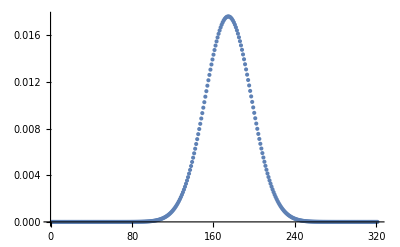

{{175}}

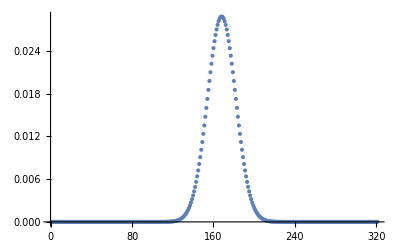

{{168}}

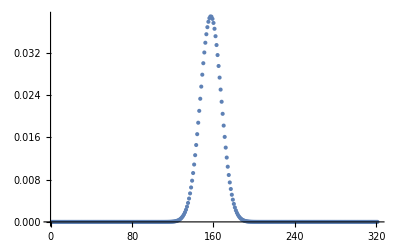

{{157}}

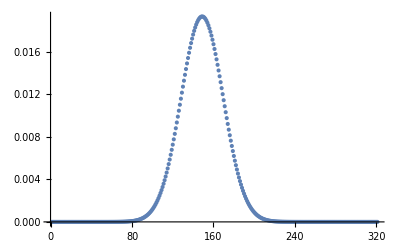

{{149}}

```mathematica
(*(*Counting Occurence*)
For[i=1,i<xsize+1,i++,
event1[[Round[(xquad[[i]]-mx)/slice]+bin/2]]=event1[[Round[(xquad[[i]]-mx)/slice]+bin/2]]+1;]

For[i=1,i<psize+1,i++,
event3[[Round[(pquad[[i]]-mp)/slice]+bin/2]]=event3[[Round[(pquad[[i]]-mp)/slice]+bin/2]]+1;]

(*Normalization*)
event1=event1/xsize;
event3=event3/psize;*)

(*Gmn is imported, discretized and normalized occurence of event*)
G={event1,event2,event3,event4}//N;
ListPlot[event1, PlotRange->Full]
Position[event1,_?(#==Max[event1]&)]
ListPlot[event2, PlotRange->Full]
Position[event2,_?(#==Max[event2]&)]
ListPlot[event3,PlotRange->Full]
Position[event3,_?(#==Max[event3]&)]
ListPlot[event4, PlotRange->Full]
Position[event4,_?(#==Max[event4]&)]
```

## Normalization Parameter for Projector

```mathematica
hermite0=Table[(psi[0,(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
norm=Sum[hermite0[[i]],{i,1,bin+1}];
norm//N
hermite0=hermite0/norm;
```

20.

## Projector Represented in quadrature basis

```mathematica
(*Matrix Element in Fock basis*)
Π=Table[(Tpsi[[a+1]]Tpsi[[b+1]]/norm)ⅇ^(ⅈ(b-a)θ),{a,0,n},{b,0,n}] ;
```

## Discretize X and θ

```mathematica
theta={0,Pi/4,Pi/2,3*Pi/4};
quad=Subdivide[-n,n,bin];
```

## Deviation Function

```mathematica
Q=Re[
Sum[(      G[[j,i]]-(  Tr[Π.ρ]/.{x->quad[[i]],θ->theta[[j]]}  )   )^2,{i,1,bin+1},{j,1,4}]
];
```

## Optimization Kernel

```mathematica
flat1=DeleteCases[Flatten[rr],_Integer];
flat2=DeleteCases[Flatten[-ⅈ*ii],_Integer];
kernel=Join[flat1,flat2];
```

## Maximum Entropy reconstruction

```mathematica
Timing[solution=FindMinimum[Q,kernel];]

Chop[ρ /. solution[[2]] ];

Chop[MatrixForm[ρ /. solution[[2]]]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{150.197,Null}

(0.763674 | 0.197665-0.0656223 ⅈ | 0.243445-0.123202 ⅈ | 0.0815502-0.0973532 ⅈ | 0.0619104-0.0940293 ⅈ | 0.0150952-0.0566564 ⅈ | 0.0004335-0.0343357 ⅈ | 0.000793811-0.0236429 ⅈ | -0.00525696+0.000770831 ⅈ
0.197665+0.0656223 ⅈ | 0.0674599 | 0.0767804-0.00862665 ⅈ | 0.0352451-0.0209194 ⅈ | 0.0291491-0.0232499 ⅈ | 0.0127008-0.0178861 ⅈ | 0.00410568-0.0127079 ⅈ | 0.0039181-0.00842848 ⅈ | -0.00189514-0.000516415 ⅈ
0.243445+0.123202 ⅈ | 0.0767804+0.00862665 ⅈ | 0.100108 | 0.0430379-0.0194741 ⅈ | 0.0357769-0.0224562 ⅈ | 0.0143565-0.018129 ⅈ | 0.0059881-0.0120266 ⅈ | 0.00441944-0.00860633 ⅈ | -0.00207967-0.000720778 ⅈ
0.0815502+0.0973532 ⅈ | 0.0352451+0.0209194 ⅈ | 0.0430379+0.0194741 ⅈ | 0.0258076 | 0.0225394-0.00348353 ⅈ | 0.012064-0.00637518 ⅈ | 0.00627145-0.00658291 ⅈ | 0.00490716-0.00415489 ⅈ | -0.00108061-0.000881255 ⅈ
0.0619104+0.0940293 ⅈ | 0.0291491+0.0232499 ⅈ | 0.0357769+0.0224562 ⅈ | 0.0225394+0.00348353 ⅈ | 0.0224287 | 0.01167-0.00350659 ⅈ | 0.0064478-0.00389472 ⅈ | 0.0046917-0.00251508 ⅈ | -0.000727146-0.000944676 ⅈ
0.0150952+0.0566564 ⅈ | 0.0127008+0.0178861 ⅈ | 0.0143565+0.018129 ⅈ | 0.012064+0.00637518 ⅈ | 0.01167+0.00350659 ⅈ | 0.00935634 | 0.00563335-0.00110811 ⅈ | 0.00437907-0.000602668 ⅈ | -0.000250667-0.00096118 ⅈ
0.0004335+0.0343357 ⅈ | 0.00410568+0.0127079 ⅈ | 0.0059881+0.0120266 ⅈ | 0.00627145+0.00658291 ⅈ | 0.0064478+0.00389472 ⅈ | 0.00563335+0.00110811 ⅈ | 0.00613952 | 0.00416079+0.000854429 ⅈ | 0.0000210744-0.000965961 ⅈ
0.000793811+0.0236429 ⅈ | 0.0039181+0.00842848 ⅈ | 0.00441944+0.00860633 ⅈ | 0.00490716+0.00415489 ⅈ | 0.0046917+0.00251508 ⅈ | 0.00437907+0.000602668 ⅈ | 0.00416079-0.000854429 ⅈ | 0.0047604 | 6.05523×10^-6-0.00107228 ⅈ
-0.00525696-0.000770831 ⅈ | -0.00189514+0.000516415 ⅈ | -0.00207967+0.000720778 ⅈ | -0.00108061+0.000881255 ⅈ | -0.000727146+0.000944676 ⅈ | -0.000250667+0.00096118 ⅈ | 0.0000210744+0.000965961 ⅈ | 6.05523×10^-6+0.00107228 ⅈ | 0.000265707)

## Plotting Real part of Density Matrix

```mathematica
DiscretePlot3D[Abs@Re[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Plotting Imaginary part

```mathematica
DiscretePlot3D[Abs@Im[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Wigner Reconstruction

```mathematica
g=2;
M=n+1;
xrange={-5,5};
yrange={-5,5};
linespace=500;
rho=ρ /. solution[[2]];
%//MatrixForm;
meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]}
{xx,yy}=meshgrid[Array[#&,linespace,xrange],Array[#&,linespace,yrange]];
aa=0.5*g*(xx+ⅈ yy);
%//MatrixForm;
wlist=Table[Table[Table[0,{i,1,M}],{j,1,M}],{k,1,M}];
wlist[[1]]=Exp[-2 Abs[aa]^2]/π;
W=Re[rho[[1,1]]]*Re[wlist[[1]]];

For[nn=1, nn<M,nn++,
wlist[[nn+1]]=(2.0*aa*wlist[[nn]])/√nn;
W+=2*Re[rho[[1,nn+1]]*wlist[[nn+1]]];
]


For[mm=1, mm<M,mm++,

temp=wlist[[mm+1]];
wlist[[mm+1]]=(2*Conjugate[aa]*temp-√mm*wlist[[mm]])/√mm;
W+=Re[rho[[mm+1,mm+1]]*wlist[[mm+1]]];
For[nn=mm+1, nn<M,nn++,
temp2=(2*aa*wlist[[nn]]-√mm*temp)/√nn;
temp=wlist[[nn+1]];
wlist[[nn+1]]=temp2;
W+=2*Re[rho[[mm+1,nn+1]]*wlist[[nn+1]]];
]
]
list=0.5*W*g^2;
pos=Position[list,_?(#==Max[list]&)]
Min[list]
disp=Sqrt[((250-pos[[1,1]])/50)^2+((250-pos[[1,2]])/50)^2]//N
ListPlot3D[0.5*W*g^2,PlotRange->All, Boxed->False,DataRange->{{-5,5},{-5,5}}]
```

{{257,273}}

-0.0131239

0.480833

-Graphics3D-